{{A11(t)→InterpolatingFunction[…](t),A12(t)→InterpolatingFunction[…](t),A13(t)→InterpolatingFunction[…](t),A21(t)→InterpolatingFunction[…](t),A22(t)→InterpolatingFunction[…](t),A23(t)→InterpolatingFunction[…](t),A31(t)→InterpolatingFunction[…](t),A32(t)→InterpolatingFunction[…](t),A33(t)→InterpolatingFunction[…](t)}}

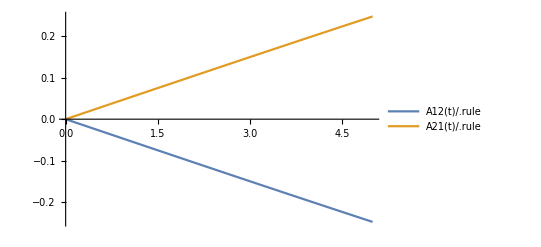

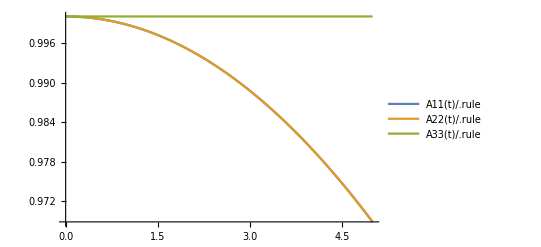

```mathematica
ClearAll["Global`*"]

Id=IdentityMatrix[3];
A[t_]:=({{A11[t], A12[t], A13[t]}, {A21[t], A22[t], A23[t]}, {A31[t], A32[t], A33[t]}});
G[t_]:=Simplify[Transpose[A[t]].A[t]];
devG[t_]:=Simplify[G[t]-1/3 Tr[G[t]]Id];
S [t_]:=Simplify[ -3/τ Det[A[t]]^(5/3)A[t].devG[t]];
τ=10^-6;

X[t_]:=Flatten[A[t]];
F[t_]:={0,c A11[t],0,0,c A21[t],0,0,c A31[t],0}; c=0.1;
Src[t_]:=Flatten[S[t]];


EQN={D[X[t],t]+F[t]==Src[t]};
IC={X[0]=={1,0,0,0,1,0,0,0,1}};


ODE=Union[EQN,IC];
{rule}=NDSolve[ODE,X[t],{t,0,10}]
Plot[{A12[t]/.rule,A21[t]/.rule},{t,0,5},PlotLegends->"Expressions"]
Plot[{A11[t]/.rule,A22[t]/.rule,A33[t]/.rule},{t,0,5},PlotLegends->"Expressions"]
```

```mathematica
NDSolve[ODE,X[t],{t,0,1}]
```

{{A11(t)→InterpolatingFunction[…](t),A12(t)→InterpolatingFunction[…](t),A13(t)→InterpolatingFunction[…](t),A21(t)→InterpolatingFunction[…](t),A22(t)→InterpolatingFunction[…](t),A23(t)→InterpolatingFunction[…](t),A31(t)→InterpolatingFunction[…](t),A32(t)→InterpolatingFunction[…](t),A33(t)→InterpolatingFunction[…](t)}}

```mathematica
EQN
IC
```

{{a'(t)(1,1),a'(t)(1,2),a'(t)(1,3),a'(t)(2,1),a'(t)(2,2),a'(t)(2,3),a'(t)(3,1),a'(t)(3,2),a'(t)(3,3)}=={-a(t)(1,1),-a(t)(1,2),-a(t)(1,3),-a(t)(2,1),-a(t)(2,2),-a(t)(2,3),-a(t)(3,1),-a(t)(3,2),-a(t)(3,3)}}

{{a(0)(1,1),a(0)(1,2),a(0)(1,3),a(0)(2,1),a(0)(2,2),a(0)(2,3),a(0)(3,1),a(0)(3,2),a(0)(3,3)}=={0,0,0,0,0,0,0,0,0}}

```mathematica
ODE
```

{{A11(0),A12(0),A13(0),A21(0),A22(0),A23(0),A31(0),A32(0),A33(0)}=={0,0,1,0,0,1,0,0,1},{A11'(t),0.1 A11(t)+A12'(t),A13'(t),A21'(t),0.1 A21(t)+A22'(t),A23'(t),A31'(t),0.1 A31(t)+A32'(t),A33'(t)}=={-1/τ 3 (A13(t) (A21(t) A32(t)-A22(t) A31(t))+A12(t) (A23(t) A31(t)-A21(t) A33(t))+A11(t) (A22(t) A33(t)-A23(t) A32(t)))^(5/3) ((2 (A11(t))^3)/3+1/3 (2 (A12(t))^2+2 (A13(t))^2+2 (A21(t))^2-(A22(t))^2-(A23(t))^2+2 (A31(t))^2-(A32(t))^2-(A33(t))^2) A11(t)+A12(t) (A21(t) A22(t)+A31(t) A32(t))+A13(t) (A21(t) A23(t)+A31(t) A33(t))),-1/τ(A13(t) (A21(t) A32(t)-A22(t) A31(t))+A12(t) (A23(t) A31(t)-A21(t) A33(t))+A11(t) (A22(t) A33(t)-A23(t) A32(t)))^(5/3) (2 (A12(t))^3+2 (A11(t))^2 A12(t)+(2 (A13(t))^2-(A21(t))^2+2 (A22(t))^2-(A23(t))^2-(A31(t))^2+2 (A32(t))^2-(A33(t))^2) A12(t)+3 A11(t) (A21(t) A22(t)+A31(t) A32(t))+3 A13(t) (A22(t) A23(t)+A32(t) A33(t))),-1/τ(A13(t) (A21(t) A32(t)-A22(t) A31(t))+A12(t) (A23(t) A31(t)-A21(t) A33(t))+A11(t) (A22(t) A33(t)-A23(t) A32(t)))^(5/3) (2 A13(t) (A11(t))^2+3 (A21(t) A23(t)+A31(t) A33(t)) A11(t)+2 (A12(t))^2 A13(t)+3 A12(t) (A22(t) A23(t)+A32(t) A33(t))+A13(t) (2 (A13(t))^2-(A21(t))^2-(A22(t))^2+2 (A23(t))^2-(A31(t))^2-(A32(t))^2+2 (A33(t))^2)),-1/τ 3 (A13(t) (A21(t) A32(t)-A22(t) A31(t))+A12(t) (A23(t) A31(t)-A21(t) A33(t))+A11(t) (A22(t) A33(t)-A23(t) A32(t)))^(5/3) (A22(t) (A11(t) A12(t)+A21(t) A22(t)+A31(t) A32(t))+A23(t) (A11(t) A13(t)+A21(t) A23(t)+A31(t) A33(t))+1/3 A21(t) (2 (A11(t))^2-(A12(t))^2-(A13(t))^2+2 (A21(t))^2-(A22(t))^2-(A23(t))^2+2 (A31(t))^2-(A32(t))^2-(A33(t))^2)),-1/τ 3 (A13(t) (A21(t) A32(t)-A22(t) A31(t))+A12(t) (A23(t) A31(t)-A21(t) A33(t))+A11(t) (A22(t) A33(t)-A23(t) A32(t)))^(5/3) (A21(t) (A11(t) A12(t)+A21(t) A22(t)+A31(t) A32(t))+A23(t) (A12(t) A13(t)+A22(t) A23(t)+A32(t) A33(t))+1/3 A22(t) (-(A11(t))^2+2 (A12(t))^2-(A13(t))^2-(A21(t))^2+2 (A22(t))^2-(A23(t))^2-(A31(t))^2+2 (A32(t))^2-(A33(t))^2)),-1/τ 3 (A13(t) (A21(t) A32(t)-A22(t) A31(t))+A12(t) (A23(t) A31(t)-A21(t) A33(t))+A11(t) (A22(t) A33(t)-A23(t) A32(t)))^(5/3) (A21(t) (A11(t) A13(t)+A21(t) A23(t)+A31(t) A33(t))+A22(t) (A12(t) A13(t)+A22(t) A23(t)+A32(t) A33(t))+1/3 A23(t) (-(A11(t))^2-(A12(t))^2+2 (A13(t))^2-(A21(t))^2-(A22(t))^2+2 (A23(t))^2-(A31(t))^2-(A32(t))^2+2 (A33(t))^2)),-1/τ 3 (A13(t) (A21(t) A32(t)-A22(t) A31(t))+A12(t) (A23(t) A31(t)-A21(t) A33(t))+A11(t) (A22(t) A33(t)-A23(t) A32(t)))^(5/3) (A32(t) (A11(t) A12(t)+A21(t) A22(t)+A31(t) A32(t))+A33(t) (A11(t) A13(t)+A21(t) A23(t)+A31(t) A33(t))+1/3 A31(t) (2 (A11(t))^2-(A12(t))^2-(A13(t))^2+2 (A21(t))^2-(A22(t))^2-(A23(t))^2+2 (A31(t))^2-(A32(t))^2-(A33(t))^2)),-1/τ 3 (A13(t) (A21(t) A32(t)-A22(t) A31(t))+A12(t) (A23(t) A31(t)-A21(t) A33(t))+A11(t) (A22(t) A33(t)-A23(t) A32(t)))^(5/3) (A31(t) (A11(t) A12(t)+A21(t) A22(t)+A31(t) A32(t))+A33(t) (A12(t) A13(t)+A22(t) A23(t)+A32(t) A33(t))+1/3 A32(t) (-(A11(t))^2+2 (A12(t))^2-(A13(t))^2-(A21(t))^2+2 (A22(t))^2-(A23(t))^2-(A31(t))^2+2 (A32(t))^2-(A33(t))^2)),-1/τ 3 (A13(t) (A21(t) A32(t)-A22(t) A31(t))+A12(t) (A23(t) A31(t)-A21(t) A33(t))+A11(t) (A22(t) A33(t)-A23(t) A32(t)))^(5/3) (A31(t) (A11(t) A13(t)+A21(t) A23(t)+A31(t) A33(t))+A32(t) (A12(t) A13(t)+A22(t) A23(t)+A32(t) A33(t))+1/3 A33(t) (-(A11(t))^2-(A12(t))^2+2 (A13(t))^2-(A21(t))^2-(A22(t))^2+2 (A23(t))^2-(A31(t))^2-(A32(t))^2+2 (A33(t))^2))}}

```mathematica
DSolve[ODE,X[t],{t,0,10}]
```

DSolve[{{A11(0),A12(0),A13(0),A21(0),A22(0),A23(0),A31(0),A32(0),A33(0)}=={1,0,0,0,1,0,0,0,1},{A11'(t),0.1 A11(t)+A12'(t),A13'(t),A21'(t),0.1 A21(t)+A22'(t),A23'(t),A31'(t),0.1 A31(t)+A32'(t),A33'(t)}=={-3000000 (A13(t) (A21(t) A32(t)-A22(t) A31(t))+A12(t) (A23(t) A31(t)-A21(t) A33(t))+A11(t) (A22(t) A33(t)-A23(t) A32(t)))^(5/3) ((2 (A11(t))^3)/3+1/3 (2 (A12(t))^2+2 (A13(t))^2+2 (A21(t))^2-(A22(t))^2-(A23(t))^2+2 (A31(t))^2-(A32(t))^2-(A33(t))^2) A11(t)+A12(t) (A21(t) A22(t)+A31(t) A32(t))+A13(t) (A21(t) A23(t)+A31(t) A33(t))),-1000000 (A13(t) (A21(t) A32(t)-A22(t) A31(t))+A12(t) (A23(t) A31(t)-A21(t) A33(t))+A11(t) (A22(t) A33(t)-A23(t) A32(t)))^(5/3) (2 (A12(t))^3+2 (A11(t))^2 A12(t)+(2 (A13(t))^2-(A21(t))^2+2 (A22(t))^2-(A23(t))^2-(A31(t))^2+2 (A32(t))^2-(A33(t))^2) A12(t)+3 A11(t) (A21(t) A22(t)+A31(t) A32(t))+3 A13(t) (A22(t) A23(t)+A32(t) A33(t))),-1000000 (A13(t) (A21(t) A32(t)-A22(t) A31(t))+A12(t) (A23(t) A31(t)-A21(t) A33(t))+A11(t) (A22(t) A33(t)-A23(t) A32(t)))^(5/3) (2 A13(t) (A11(t))^2+3 (A21(t) A23(t)+A31(t) A33(t)) A11(t)+2 (A12(t))^2 A13(t)+3 A12(t) (A22(t) A23(t)+A32(t) A33(t))+A13(t) (2 (A13(t))^2-(A21(t))^2-(A22(t))^2+2 (A23(t))^2-(A31(t))^2-(A32(t))^2+2 (A33(t))^2)),-3000000 (A13(t) (A21(t) A32(t)-A22(t) A31(t))+A12(t) (A23(t) A31(t)-A21(t) A33(t))+A11(t) (A22(t) A33(t)-A23(t) A32(t)))^(5/3) (A22(t) (A11(t) A12(t)+A21(t) A22(t)+A31(t) A32(t))+A23(t) (A11(t) A13(t)+A21(t) A23(t)+A31(t) A33(t))+1/3 A21(t) (2 (A11(t))^2-(A12(t))^2-(A13(t))^2+2 (A21(t))^2-(A22(t))^2-(A23(t))^2+2 (A31(t))^2-(A32(t))^2-(A33(t))^2)),-3000000 (A13(t) (A21(t) A32(t)-A22(t) A31(t))+A12(t) (A23(t) A31(t)-A21(t) A33(t))+A11(t) (A22(t) A33(t)-A23(t) A32(t)))^(5/3) (A21(t) (A11(t) A12(t)+A21(t) A22(t)+A31(t) A32(t))+A23(t) (A12(t) A13(t)+A22(t) A23(t)+A32(t) A33(t))+1/3 A22(t) (-(A11(t))^2+2 (A12(t))^2-(A13(t))^2-(A21(t))^2+2 (A22(t))^2-(A23(t))^2-(A31(t))^2+2 (A32(t))^2-(A33(t))^2)),-3000000 (A13(t) (A21(t) A32(t)-A22(t) A31(t))+A12(t) (A23(t) A31(t)-A21(t) A33(t))+A11(t) (A22(t) A33(t)-A23(t) A32(t)))^(5/3) (A21(t) (A11(t) A13(t)+A21(t) A23(t)+A31(t) A33(t))+A22(t) (A12(t) A13(t)+A22(t) A23(t)+A32(t) A33(t))+1/3 A23(t) (-(A11(t))^2-(A12(t))^2+2 (A13(t))^2-(A21(t))^2-(A22(t))^2+2 (A23(t))^2-(A31(t))^2-(A32(t))^2+2 (A33(t))^2)),-3000000 (A13(t) (A21(t) A32(t)-A22(t) A31(t))+A12(t) (A23(t) A31(t)-A21(t) A33(t))+A11(t) (A22(t) A33(t)-A23(t) A32(t)))^(5/3) (A32(t) (A11(t) A12(t)+A21(t) A22(t)+A31(t) A32(t))+A33(t) (A11(t) A13(t)+A21(t) A23(t)+A31(t) A33(t))+1/3 A31(t) (2 (A11(t))^2-(A12(t))^2-(A13(t))^2+2 (A21(t))^2-(A22(t))^2-(A23(t))^2+2 (A31(t))^2-(A32(t))^2-(A33(t))^2)),-3000000 (A13(t) (A21(t) A32(t)-A22(t) A31(t))+A12(t) (A23(t) A31(t)-A21(t) A33(t))+A11(t) (A22(t) A33(t)-A23(t) A32(t)))^(5/3) (A31(t) (A11(t) A12(t)+A21(t) A22(t)+A31(t) A32(t))+A33(t) (A12(t) A13(t)+A22(t) A23(t)+A32(t) A33(t))+1/3 A32(t) (-(A11(t))^2+2 (A12(t))^2-(A13(t))^2-(A21(t))^2+2 (A22(t))^2-(A23(t))^2-(A31(t))^2+2 (A32(t))^2-(A33(t))^2)),-3000000 (A13(t) (A21(t) A32(t)-A22(t) A31(t))+A12(t) (A23(t) A31(t)-A21(t) A33(t))+A11(t) (A22(t) A33(t)-A23(t) A32(t)))^(5/3) (A31(t) (A11(t) A13(t)+A21(t) A23(t)+A31(t) A33(t))+A32(t) (A12(t) A13(t)+A22(t) A23(t)+A32(t) A33(t))+1/3 A33(t) (-(A11(t))^2-(A12(t))^2+2 (A13(t))^2-(A21(t))^2-(A22(t))^2+2 (A23(t))^2-(A31(t))^2-(A32(t))^2+2 (A33(t))^2))}},{A11(t),A12(t),A13(t),A21(t),A22(t),A23(t),A31(t),A32(t),A33(t)},{t,0,10}]